```mathematica
c = Cos[θ Degree];
```

```mathematica
M =({{1, c^2, c, c^2, c^2, c^3}, {c^2, 1, c, c^2, c^2, c^3}, {c, c, 1, c^3, c^3, c^4}, {-c^2, -c^2, -c^3, -1, -c^2, -c}, {-c^2, -c^2, -c^3, -c^2, -1, -c}, {-c^3, -c^3, -c^4, -c, -c, -1}});
```

```mathematica
MatrixForm[M]
```

(1 | Cos[° θ]^2 | Cos[° θ] | Cos[° θ]^2 | Cos[° θ]^2 | Cos[° θ]^3
Cos[° θ]^2 | 1 | Cos[° θ] | Cos[° θ]^2 | Cos[° θ]^2 | Cos[° θ]^3
Cos[° θ] | Cos[° θ] | 1 | Cos[° θ]^3 | Cos[° θ]^3 | Cos[° θ]^4
-Cos[° θ]^2 | -Cos[° θ]^2 | -Cos[° θ]^3 | -1 | -Cos[° θ]^2 | -Cos[° θ]
-Cos[° θ]^2 | -Cos[° θ]^2 | -Cos[° θ]^3 | -Cos[° θ]^2 | -1 | -Cos[° θ]
-Cos[° θ]^3 | -Cos[° θ]^3 | -Cos[° θ]^4 | -Cos[° θ] | -Cos[° θ] | -1)

```mathematica
({{1, c^2, c, c^2, c^2, c^3}, {c^2, 1, c, c^2, c^2, c^3}, {c, c, 1, c^3, c^3, c^4}, {-c^2, -c^2, -c^3, -1, -c^2, -c}, {-c^2, -c^2, -c^3, -c^2, -1, -c}, {-c^3, -c^3, -c^4, -c, -c, -1}})
```

{{1,Cos[° θ]^2,Cos[° θ],Cos[° θ]^2,Cos[° θ]^2,Cos[° θ]^3},{Cos[° θ]^2,1,Cos[° θ],Cos[° θ]^2,Cos[° θ]^2,Cos[° θ]^3},{Cos[° θ],Cos[° θ],1,Cos[° θ]^3,Cos[° θ]^3,Cos[° θ]^4},{-Cos[° θ]^2,-Cos[° θ]^2,-Cos[° θ]^3,-1,-Cos[° θ]^2,-Cos[° θ]},{-Cos[° θ]^2,-Cos[° θ]^2,-Cos[° θ]^3,-Cos[° θ]^2,-1,-Cos[° θ]},{-Cos[° θ]^3,-Cos[° θ]^3,-Cos[° θ]^4,-Cos[° θ],-Cos[° θ],-1}}

```mathematica
d=DiagonalMatrix[Eigenvalues[M]]
p=Transpose[Normalize/@Eigenvectors[M]];
```

{{1/2 (1-Cos[2 ° θ]),0,0,0,0,0},{0,1/2 (-1+Cos[2 ° θ]),0,0,0,0},{0,0,-√(301/256-13/32 Cos[2 ° θ]-43/64 Cos[4 ° θ]-3/32 Cos[6 ° θ]-1/256 Cos[8 ° θ]-(√((-4816+1664 Cos[2 ° θ]+2752 Cos[4 ° θ]+384 Cos[6 ° θ]+16 Cos[8 ° θ])^2-8192 (658-1000 Cos[2 ° θ]+401 Cos[4 ° θ]-36 Cos[6 ° θ]-34 Cos[8 ° θ]+12 Cos[10 ° θ]-Cos[12 ° θ])))/4096),0,0,0},{0,0,0,√(301/256-13/32 Cos[2 ° θ]-43/64 Cos[4 ° θ]-3/32 Cos[6 ° θ]-1/256 Cos[8 ° θ]-(√((-4816+1664 Cos[2 ° θ]+2752 Cos[4 ° θ]+384 Cos[6 ° θ]+16 Cos[8 ° θ])^2-8192 (658-1000 Cos[2 ° θ]+401 Cos[4 ° θ]-36 Cos[6 ° θ]-34 Cos[8 ° θ]+12 Cos[10 ° θ]-Cos[12 ° θ])))/4096),0,0},{0,0,0,0,-√(301/256-13/32 Cos[2 ° θ]-43/64 Cos[4 ° θ]-3/32 Cos[6 ° θ]-1/256 Cos[8 ° θ]+(√((-4816+1664 Cos[2 ° θ]+2752 Cos[4 ° θ]+384 Cos[6 ° θ]+16 Cos[8 ° θ])^2-8192 (658-1000 Cos[2 ° θ]+401 Cos[4 ° θ]-36 Cos[6 ° θ]-34 Cos[8 ° θ]+12 Cos[10 ° θ]-Cos[12 ° θ])))/4096),0},{0,0,0,0,0,√(301/256-13/32 Cos[2 ° θ]-43/64 Cos[4 ° θ]-3/32 Cos[6 ° θ]-1/256 Cos[8 ° θ]+(√((-4816+1664 Cos[2 ° θ]+2752 Cos[4 ° θ]+384 Cos[6 ° θ]+16 Cos[8 ° θ])^2-8192 (658-1000 Cos[2 ° θ]+401 Cos[4 ° θ]-36 Cos[6 ° θ]-34 Cos[8 ° θ]+12 Cos[10 ° θ]-Cos[12 ° θ])))/4096)}}

```mathematica
MatrixForm[d]
```

(1/2 (1-Cos[2 ° θ]) | 0 | 0 | 0 | 0 | 0
0 | 1/2 (-1+Cos[2 ° θ]) | 0 | 0 | 0 | 0
0 | 0 | -√(301/256-13/32 Cos[2 ° θ]-43/64 Cos[4 ° θ]-3/32 Cos[6 ° θ]-1/256 Cos[8 ° θ]-(√((-4816+1664 Cos[2 ° θ]+2752 Cos[4 ° θ]+384 Cos[6 ° θ]+16 Cos[8 ° θ])^2-8192 (658-1000 Cos[2 ° θ]+401 Cos[4 ° θ]-36 Cos[6 ° θ]-34 Cos[8 ° θ]+12 Cos[10 ° θ]-Cos[12 ° θ])))/4096) | 0 | 0 | 0
0 | 0 | 0 | √(301/256-13/32 Cos[2 ° θ]-43/64 Cos[4 ° θ]-3/32 Cos[6 ° θ]-1/256 Cos[8 ° θ]-(√((-4816+1664 Cos[2 ° θ]+2752 Cos[4 ° θ]+384 Cos[6 ° θ]+16 Cos[8 ° θ])^2-8192 (658-1000 Cos[2 ° θ]+401 Cos[4 ° θ]-36 Cos[6 ° θ]-34 Cos[8 ° θ]+12 Cos[10 ° θ]-Cos[12 ° θ])))/4096) | 0 | 0
0 | 0 | 0 | 0 | -√(301/256-13/32 Cos[2 ° θ]-43/64 Cos[4 ° θ]-3/32 Cos[6 ° θ]-1/256 Cos[8 ° θ]+(√((-4816+1664 Cos[2 ° θ]+2752 Cos[4 ° θ]+384 Cos[6 ° θ]+16 Cos[8 ° θ])^2-8192 (658-1000 Cos[2 ° θ]+401 Cos[4 ° θ]-36 Cos[6 ° θ]-34 Cos[8 ° θ]+12 Cos[10 ° θ]-Cos[12 ° θ])))/4096) | 0
0 | 0 | 0 | 0 | 0 | √(301/256-13/32 Cos[2 ° θ]-43/64 Cos[4 ° θ]-3/32 Cos[6 ° θ]-1/256 Cos[8 ° θ]+(√((-4816+1664 Cos[2 ° θ]+2752 Cos[4 ° θ]+384 Cos[6 ° θ]+16 Cos[8 ° θ])^2-8192 (658-1000 Cos[2 ° θ]+401 Cos[4 ° θ]-36 Cos[6 ° θ]-34 Cos[8 ° θ]+12 Cos[10 ° θ]-Cos[12 ° θ])))/4096))

```mathematica
FullSimplify[d]
```

{{Sin[° θ]^2,0,0,0,0,0},{0,-Sin[° θ]^2,0,0,0,0},{0,0,-1/16 √(301-104 Cos[2 ° θ]-172 Cos[4 ° θ]-24 Cos[6 ° θ]-Cos[8 ° θ]-4 √2 √(Cos[° θ]^2 (63766+56258 Cos[2 ° θ]+9912 Cos[4 ° θ]+1085 Cos[6 ° θ]+50 Cos[8 ° θ]+Cos[10 ° θ]) Sin[° θ]^4)),0,0,0},{0,0,0,1/16 √(301-104 Cos[2 ° θ]-172 Cos[4 ° θ]-24 Cos[6 ° θ]-Cos[8 ° θ]-4 √2 √(Cos[° θ]^2 (63766+56258 Cos[2 ° θ]+9912 Cos[4 ° θ]+1085 Cos[6 ° θ]+50 Cos[8 ° θ]+Cos[10 ° θ]) Sin[° θ]^4)),0,0},{0,0,0,0,-1/16 √(301-104 Cos[2 ° θ]-172 Cos[4 ° θ]-24 Cos[6 ° θ]-Cos[8 ° θ]+4 √2 √(Cos[° θ]^2 (63766+56258 Cos[2 ° θ]+9912 Cos[4 ° θ]+1085 Cos[6 ° θ]+50 Cos[8 ° θ]+Cos[10 ° θ]) Sin[° θ]^4)),0},{0,0,0,0,0,1/16 √(301-104 Cos[2 ° θ]-172 Cos[4 ° θ]-24 Cos[6 ° θ]-Cos[8 ° θ]+4 √2 √(Cos[° θ]^2 (63766+56258 Cos[2 ° θ]+9912 Cos[4 ° θ]+1085 Cos[6 ° θ]+50 Cos[8 ° θ]+Cos[10 ° θ]) Sin[° θ]^4))}}

```mathematica
MatrixForm[%8]
```

(1)
 |  |  |  |

```mathematica
sum = 2 (1-c^2) + 2 ((Sqrt[-((-1+c^2) (2+c (8 c+5 c^3+c^5+Sqrt[32+100 c^2+68 c^4+45 c^6+10 c^8+c^10])))]/Sqrt[2])) + 2 ((Sqrt[-((-1+c^2) (2+8 c^2+5 c^4+c^6-c Sqrt[32+100 c^2+68 c^4+45 c^6+10 c^8+c^10]))]/Sqrt[2]));
```

```mathematica
%36
```

2 (1-Cos[° θ]^2)+√2 √(-((-1+Cos[° θ]^2) (2+8 Cos[° θ]^2+5 Cos[° θ]^4+Cos[° θ]^6-Cos[° θ] √(32+100 Cos[° θ]^2+68 Cos[° θ]^4+45 Cos[° θ]^6+10 Cos[° θ]^8+Cos[° θ]^10))))+√2 √(-((-1+Cos[° θ]^2) (2+Cos[° θ] (8 Cos[° θ]+5 Cos[° θ]^3+Cos[° θ]^5+√(32+100 Cos[° θ]^2+68 Cos[° θ]^4+45 Cos[° θ]^6+10 Cos[° θ]^8+Cos[° θ]^10)))))

```mathematica
FullSimplify[1/3 *sum]|
```

```mathematica
prob = 1/2 + 1/4 *(FullSimplify[1/3*sum])
```

```mathematica
1/2+1/12 (1-Cos[2 ° θ]+√2 √((2+8 Cos[° θ]^2+5 Cos[° θ]^4+Cos[° θ]^6-Cos[° θ] √(32+100 Cos[° θ]^2+68 Cos[° θ]^4+45 Cos[° θ]^6+10 Cos[° θ]^8+Cos[° θ]^10)) Sin[° θ]^2)+√2 √((2+Cos[° θ] (8 Cos[° θ]+5 Cos[° θ]^3+Cos[° θ]^5+√(32+100 Cos[° θ]^2+68 Cos[° θ]^4+45 Cos[° θ]^6+10 Cos[° θ]^8+Cos[° θ]^10))) Sin[° θ]^2))
```

1/2+1/12 (1-Cos[2 ° θ]+√2 √((2+8 Cos[° θ]^2+5 Cos[° θ]^4+Cos[° θ]^6-Cos[° θ] √(32+100 Cos[° θ]^2+68 Cos[° θ]^4+45 Cos[° θ]^6+10 Cos[° θ]^8+Cos[° θ]^10)) Sin[° θ]^2)+√2 √((2+Cos[° θ] (8 Cos[° θ]+5 Cos[° θ]^3+Cos[° θ]^5+√(32+100 Cos[° θ]^2+68 Cos[° θ]^4+45 Cos[° θ]^6+10 Cos[° θ]^8+Cos[° θ]^10))) Sin[° θ]^2))

```mathematica
FullSimplify[prob]
```

-1/12 Cos[2 ° θ]+1/12 (7+√2 √((2+8 Cos[° θ]^2+5 Cos[° θ]^4+Cos[° θ]^6-Cos[° θ] √(32+100 Cos[° θ]^2+68 Cos[° θ]^4+45 Cos[° θ]^6+10 Cos[° θ]^8+Cos[° θ]^10)) Sin[° θ]^2)+√2 √((2+Cos[° θ] (8 Cos[° θ]+5 Cos[° θ]^3+Cos[° θ]^5+√(32+100 Cos[° θ]^2+68 Cos[° θ]^4+45 Cos[° θ]^6+10 Cos[° θ]^8+Cos[° θ]^10))) Sin[° θ]^2))

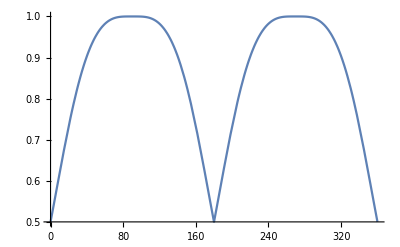

```mathematica
Plot[prob,{θ,0,360}]
```

```mathematica
Show[Plot[prob,{θ,0,360}],AxesLabel->{HoldForm[θ],HoldForm[Probability]},PlotLabel->HoldForm[Entanglment probability],LabelStyle->{GrayLevel[0]}]
```

```mathematica
prob2 = 1/2(1+ (2/3  Sin[2 θ] + 1/3 Sin[4 θ]))
```

1/2 (1+2/3 Sin[2 θ]+1/3 Sin[4 θ])

```mathematica
Simplify[prob2]
```

1/6 (3+2 Sin[2 θ]+Sin[4 θ])

```mathematica
TrigToExp[1/6 (3+2 Sin[2 θ]+Sin[4 θ])]
```

1/2+1/6 ⅈ ⅇ^(-2 ⅈ θ)-1/6 ⅈ ⅇ^(2 ⅈ θ)+1/12 ⅈ ⅇ^(-4 ⅈ θ)-1/12 ⅈ ⅇ^(4 ⅈ θ)

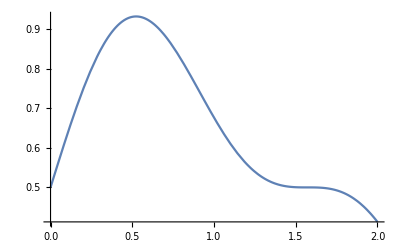

```mathematica
Plot[prob2,{θ,0,2}]
```

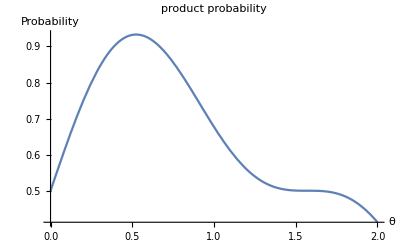

1/2+1/384 √(301-104 Cos[2 ° θ]-172 Cos[4 ° θ]-24 Cos[6 ° θ]-Cos[8 ° θ]-4 √2 √(Cos[° θ]^2 (63766+56258 Cos[2 ° θ]+9912 Cos[4 ° θ]+1085 Cos[6 ° θ]+50 Cos[8 ° θ]+Cos[10 ° θ]) Sin[° θ]^4))

```mathematica
Show[Plot[prob2,{θ,0,2}],AxesLabel->{HoldForm[θ],HoldForm[Probability]},PlotLabel->HoldForm[product probability],LabelStyle->{GrayLevel[0]}]

prob4 = 1/2 + 1/4 *(FullSimplify[1/3*1/2 (√(301/256-13/32 Cos[2 ° θ]-43/64 Cos[4 ° θ]-3/32 Cos[6 ° θ]-1/256 Cos[8 ° θ]+(√((-4816+1664 Cos[2 ° θ]+2752 Cos[4 ° θ]+384 Cos[6 ° θ]+16 Cos[8 ° θ])^2-8192 (658-1000 Cos[2 ° θ]+401 Cos[4 ° θ]-36 Cos[6 ° θ]-34 Cos[8 ° θ]+12 Cos[10 ° θ]-Cos[12 ° θ])))/4096))])
```

```mathematica
1/2+1/12 Sin[° θ]^2
```

1/2+1/12 Sin[° θ]^2

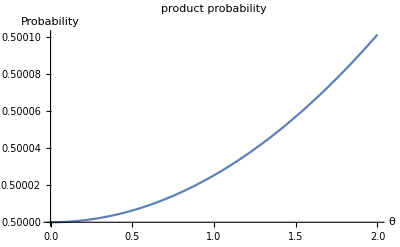

```mathematica
Show[Plot[prob3,{θ,0,2}],AxesLabel->{HoldForm[θ],HoldForm[Probability]},PlotLabel->HoldForm[product probability],LabelStyle->{GrayLevel[0]}]
```

```mathematica
prob3 = 1/2 + 1/4 *(FullSimplify[1/3*1/2 (1-Cos[2 ° θ])]
```

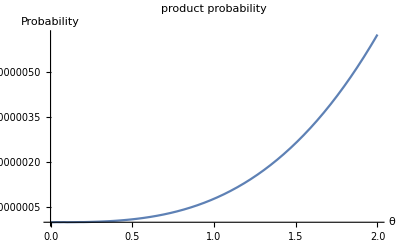

```mathematica
Show[Plot[prob4,{θ,0,2}],AxesLabel->{HoldForm[θ],HoldForm[Probability]},PlotLabel->HoldForm[product probability],LabelStyle->{GrayLevel[0]}]
```

```mathematica
prob5= 1/2 + 1/4 *(FullSimplify[1/3*1/2 (√(301/256-13/32 Cos[2 ° θ]-43/64 Cos[4 ° θ]-3/32 Cos[6 ° θ]-1/256 Cos[8 ° θ]+(√((-4816+1664 Cos[2 ° θ]+2752 Cos[4 ° θ]+384 Cos[6 ° θ]+16 Cos[8 ° θ])^2-8192 (658-1000 Cos[2 ° θ]+401 Cos[4 ° θ]-36 Cos[6 ° θ]-34 Cos[8 ° θ]+12 Cos[10 ° θ]-Cos[12 ° θ])))/4096))])
```

1/2+1/384 √(301-104 Cos[2 ° θ]-172 Cos[4 ° θ]-24 Cos[6 ° θ]-Cos[8 ° θ]+4 √2 √(Cos[° θ]^2 (63766+56258 Cos[2 ° θ]+9912 Cos[4 ° θ]+1085 Cos[6 ° θ]+50 Cos[8 ° θ]+Cos[10 ° θ]) Sin[° θ]^4))

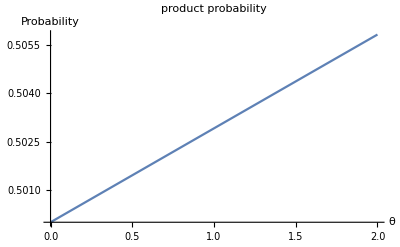

```mathematica
Show[Plot[prob5,{θ,0,2}],AxesLabel->{HoldForm[θ],HoldForm[Probability]},PlotLabel->HoldForm[product probability],LabelStyle->{GrayLevel[0]}]
```